```mathematica
<<Vilcretas`
```

VilCretas está disponible.

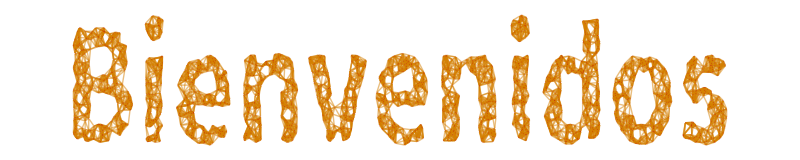

```mathematica
GrafoString["Bienvenidos"]
```

```mathematica
RecPila[n_]:=If[n==5, 2, 5*RecPila[n-1]+2*n-√2]
```

```mathematica
RecAux[n_,cont_:5, a1_:2]:=If[n==5, 2, If[n==cont, a1,
RecAux[n, cont +1, 5*a1+2*(cont + 1)-√2]]]
```

```mathematica
RecCola[n_]:=
Module[{recAux},
recAux[k_, cont_:5, a1_]:=If[k==5, 2, If[k==cont, a1,
recAux[k, cont +1, 5*a1+2*(cont + 1)-√2]]];
recAux[n, 2]
]
```

```mathematica
Table[RecCola[i]==RecPila[i], {i,5, 10}]
```

{True,True,True,True,True,True}

```mathematica
a[n_]:= a[n-1]+6*a[n-2]
a[1]=-10;
a[2]= -19;
```

```mathematica
a[3]
```

```mathematica
-79
```

```mathematica
RecCola[n_]:=Module[
{recAux},
(*
Receta: 
k=limite, 
  cont= contador, inicia en el mayor caso base posible
 Vamos a tener tantos parametros a, como n casos base tengamos
*)
recAux[k_, cont_:2, a1_,a2_]:=
If[k==1, -10, If[k==2, -19, If[k==cont,a2,
recAux[k,cont+ 1, a2, a2+6 * a1]]]];
recAux[n, -10, -19]
]
```

# Examenes

Caso base: n + 3 = 4
n = 4 - 3
n = 1
Resultado del caso base:

```mathematica
(17*4^2+12)/(11*4-2^(-2*4)+8)
```

72704/13311

Caso base:
2 = n-8
10=n
Resultado base:

```mathematica
(13^(5*2)-9)/(5*2^3+8)
```

8616155740/3

```mathematica
Simplify[3+n-8]
```

-5+n

```mathematica
a[n_]:=If[n==3,6/5, 2 n^2-35*n*a[n-1]]
```